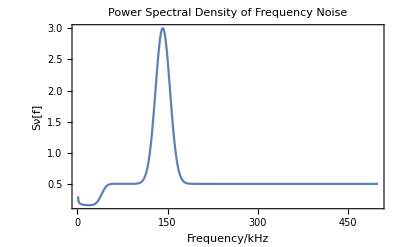

```mathematica
a=0.5(1+0.3/f)+1*0.35/2(Erf[(f-40)/10]-1)+75.2/(Sqrt[2π]σservo)Exp[-(f-fcenter)^2/(2 σservo^2)];
p1=Plot[a,{f,1,500},PlotRange->All,Frame->True,FrameLabel->{Style["Frequency/kHz",Bold,16],Style["Sν[f]",Bold,16]},PlotLabel->Style["Power Spectral Density of Frequency Noise",Bold,16]]
```